```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
transeries=Transpose[series];
transeries=Drop[transeries,1];
Dimensions[transeries]
hopdates=Drop[series[[1]],4]
%//Length
countriescsv=transeries[[1]];
%//Dimensions
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

{98,265}

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20,4/19/20,4/20/20,4/21/20,4/22/20,4/23/20,4/24/20,4/25/20}

95

{265}

```mathematica
TableForm[transeries];
```

```mathematica
CountryData["Japan","Population"]
```

126225259

```mathematica
{"Singapore",200,{2.835279843883035*^8,64.38918662693713,0.1259411788554341},21,7,10,0},
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0},
```

```mathematica
countryparameters=
(*name,truncdrop,jp0,lag,projtime,bootlag,plotdrop*)
{
{"Canada",200,{52180.39484847384,1005.9304582251706,0.1324225337960489},21,21,10,0},{"Australia",100,{6540.8364412808105,85.77223261633138,0.2345420078562459},21,21,10,0},{"New Zealand",5,{1441.2482649030032,14.971640930135235,0.23959274221723975},21,21,10,0},{"Croatia",10,{1985.7723787465545,21.596481176857367,0.1589401951808019},21,21,10,5},{"Czechia",10,{7096.988271837173,68.14371590582019,0.16461693785708748},21,21,10,5},
{"Sweden",200,{23138.83457722449,461.922977379802,0.10293773671900139},28,14,10,0},
{"Greece",50,{2469.7252428688025,97.9216579531985,0.1381653045706424},28,21,10,0},
{"Japan",950,{17986.663577976567,576.9474735585374,0.12382285884487645},28,14,8,0},
{"Denmark",1100,{9249.181828199724,848.3550476707888,0.11809736637519559},28,14,10,0}
}
```

{{Canada,200,{52180.4,1005.93,0.132423},21,21,10,0},{Australia,100,{6540.84,85.7722,0.234542},21,21,10,0},{New Zealand,5,{1441.25,14.9716,0.239593},21,21,10,0},{Croatia,10,{1985.77,21.5965,0.15894},21,21,10,5},{Czechia,10,{7096.99,68.1437,0.164617},21,21,10,5},{Sweden,200,{23138.8,461.923,0.102938},28,14,10,0},{Greece,50,{2469.73,97.9217,0.138165},28,21,10,0},{Japan,950,{17986.7,576.947,0.123823},28,14,8,0},{Denmark,1100,{9249.18,848.355,0.118097},28,14,10,0}}

```mathematica
Export["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml",countryparameters]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml

```mathematica
countryparameters=Import["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml"]
```

{{Spain,300,{215676.,3181.5,0.148262},28,14,10,0},{Canada,200,{54700.6,1073.56,0.12833},21,21,10,0},{Australia,100,{6563.71,88.1183,0.232672},21,21,10,0},{New Zealand,5,{1447.14,15.4045,0.237648},21,21,10,0},{Croatia,10,{2017.72,23.1855,0.15542},21,21,10,5},{Czechia,10,{7216.09,74.357,0.160426},21,21,10,5},{Sweden,200,{23138.8,461.923,0.102938},28,14,10,0},{Greece,50,{2469.73,97.9217,0.138165},28,21,10,0},{Japan,950,{17951.8,517.917,0.123382},28,14,8,0}}

```mathematica
"Spain",
```

```mathematica
wolfcountrynames={"Canada","Australia","New Zealand","Croatia","CzechRepublic","Sweden","Greece","Japan","Denmark"};
wpopulations=Map[CountryData[#,"Population"][[1]]&,wolfcountrynames]
```

{35309555,23502754,4554858,4369961,10611300,9595619,11470255,126225259,5628958}

```mathematica
countrybootabcs={};
```

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump

country : Canada

data length : 42

start date : {2020,3,15}

jdp0 : {54700.6,1073.56,0.12833}

jp20 : {79963.2,2786.26,0.0864348}

backward result : {19758.,271.885,0.236761}

forward result : {79963.2,2786.26,0.0864348}

last tab: {79963.2,2786.26,0.0864348}

backward result : {19758.,271.885,0.236761}

forward result : {79963.2,2786.26,0.0864348}

past errors : {{2134.73,3379.5,4248.96,4934.97,6443.72,7739.07,9597.92,10900.4,11382.1,12573.1},7333.45}

boot tab : {{45958.,1054.91,0.134768},{40407.8,945.221,0.143658},{47853.4,1228.12,0.127235},{57811.7,1588.9,0.112084},{69239.7,1966.02,0.100293},{78771.6,2323.94,0.09197},{96797.3,2734.07,0.0835357},{120698.,3158.03,0.0763972},{181377.,3636.83,0.0690361},{229279.,3962.76,0.0651954},{196978.,4123.38,0.0646047},{194337.,4345.05,0.0631347}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42}

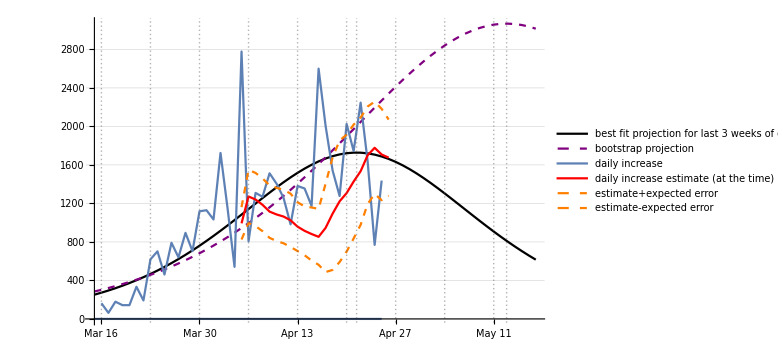

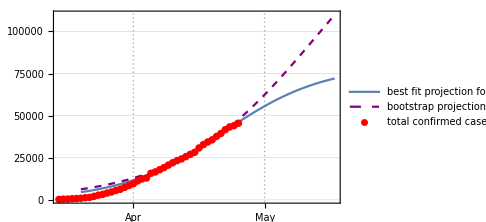

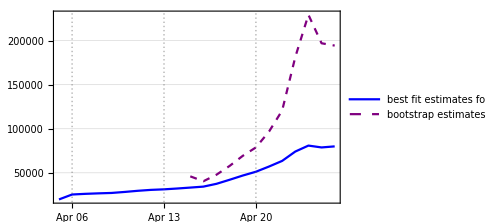

April 26

Canadadate.txt

Canadagraf.png

Canadaloggraf.png

Canadadfgraf.png

Canadafinalplot.png

country : Australia

data length : 47

start date : {2020,3,10}

jdp0 : {6563.71,88.1183,0.232672}

jp20 : {6766.44,715.256,0.140475}

backward result : {6333.48,61.3826,0.258068}

forward result : {6766.44,715.256,0.140475}

last tab: {6766.44,715.256,0.140475}

backward result : {6333.48,61.3826,0.258068}

forward result : {6766.44,715.256,0.140475}

past errors : {{43.9967,88.4563,121.935,153.855,158.746,174.226,175.986,181.777,193.396,207.681},150.006}

boot tab : {{6236.05,65.0561,0.254921},{6538.97,99.7277,0.227185},{6680.96,127.765,0.212343},{6659.47,126.959,0.213015},{6685.33,145.069,0.206255},{6716.95,169.703,0.198415},{6739.39,206.803,0.189174},{6767.52,252.699,0.179859},{6868.31,385.44,0.159561},{6930.96,513.821,0.14614},{6988.52,689.771,0.132765},{6950.09,730.47,0.131633},{6956.65,930.089,0.122078},{7011.34,1279.75,0.10784},{7030.75,1582.12,0.0988361},{7051.54,1928.15,0.0901406},{7033.47,2055.46,0.0881846}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47}

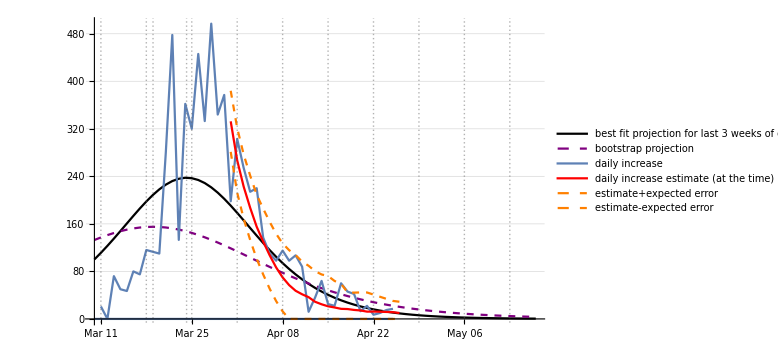

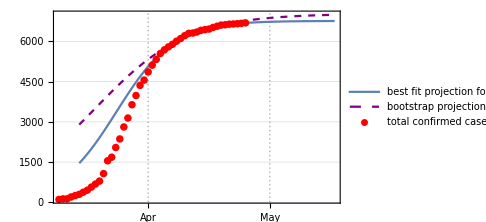

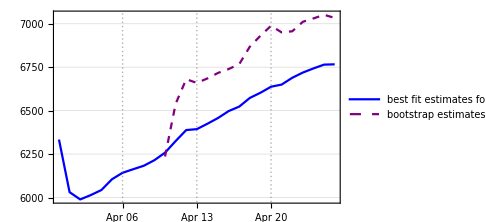

April 26

Australiadate.txt

Australiagraf.png

Australialoggraf.png

Australiadfgraf.png

Australiafinalplot.png

country : New Zealand

data length : 43

start date : {2020,3,14}

jdp0 : {1447.14,15.4045,0.237648}

jp20 : {1473.24,44.2775,0.190567}

backward result : {981.19,4.49853,0.341492}

forward result : {1473.24,44.2775,0.190567}

last tab: {1473.24,44.2775,0.190567}

backward result : {981.19,4.49853,0.341492}

forward result : {1473.24,44.2775,0.190567}

past errors : {{1.58158,-0.0740539,5.08848,7.7421,11.6132,12.4746,15.1395,17.4545,20.2948,27.5587},11.8873}

boot tab : {{1833.01,53.1616,0.158085},{1745.34,52.5281,0.161741},{1653.58,49.0838,0.169019},{1584.85,44.396,0.177548},{1536.2,38.8581,0.18697},{1509.47,34.2446,0.194769},{1500.49,32.6958,0.197606},{1488.29,29.0462,0.2039},{1478.53,26.5983,0.208752},{1482.16,31.3381,0.201653},{1481.68,34.8448,0.197617},{1486.04,47.1765,0.185404},{1494.82,73.9462,0.167186}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43}

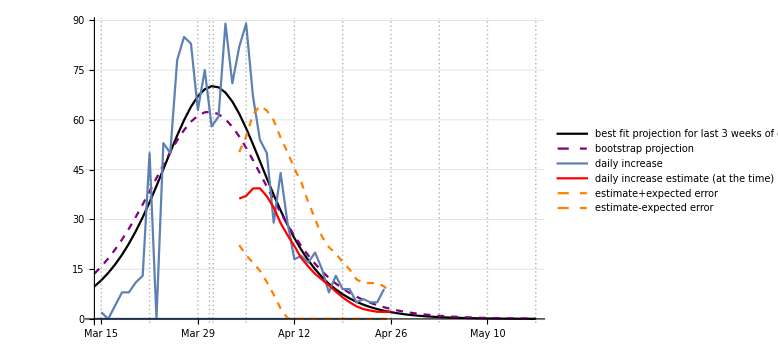

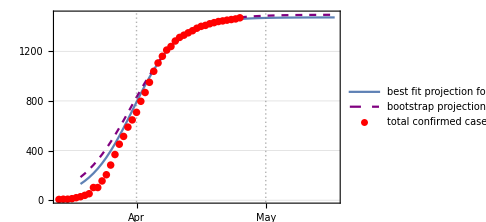

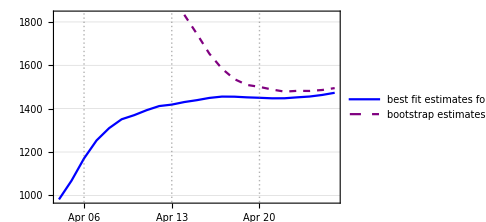

April 26

newzealanddate.txt

newzealandgraf.png

newzealandloggraf.png

newzealanddfgraf.png

newzealandfinalplot.png

country : Croatia

data length : 51

start date : {2020,3,6}

jdp0 : {2017.72,23.1855,0.15542}

jp20 : {2139.68,46.789,0.128103}

backward result : {835.937,1.62704,0.316962}

forward result : {2139.68,46.789,0.128103}

last tab: {2139.68,46.789,0.128103}

backward result : {835.937,1.62704,0.316962}

forward result : {2139.68,46.789,0.128103}

past errors : {{27.6401,16.9528,4.30863,15.5397,0.463671,4.89063,26.6282,39.4861,51.2794,43.8311},23.102}

boot tab : {{1753.63,15.3017,0.178544},{1699.93,15.2697,0.179765},{1759.03,17.9074,0.171919},{1918.37,24.168,0.156701},{2031.8,30.4091,0.145864},{2234.16,41.1379,0.131574},{2212.36,46.4471,0.12736},{2419.65,61.3622,0.114706},{2598.91,77.5604,0.104611},{2869.15,98.1151,0.0943032},{3065.29,117.977,0.0868374},{3424.2,144.853,0.0782348},{3431.63,159.817,0.0751471},{3255.65,166.798,0.0748764},{3196.99,179.479,0.0731036},{2820.71,167.394,0.0783883},{2641.69,157.695,0.0823438},{2493.49,137.335,0.0886636},{2381.1,117.462,0.0953606},{2286.,92.5786,0.104378},{2191.95,63.4271,0.117748}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51}

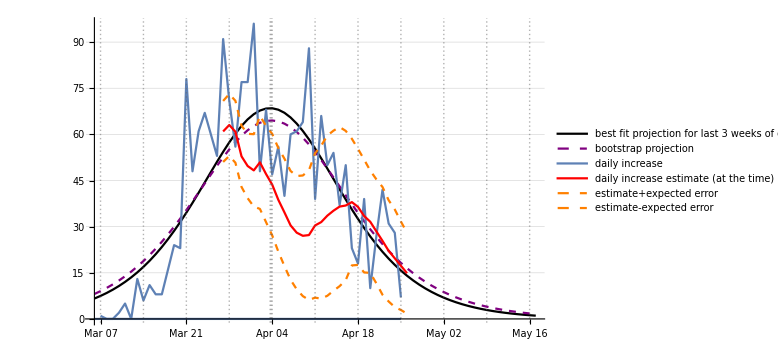

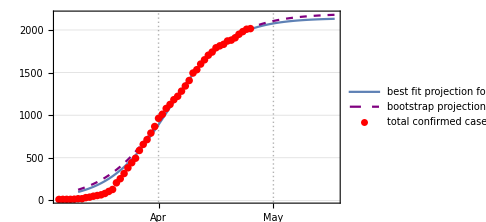

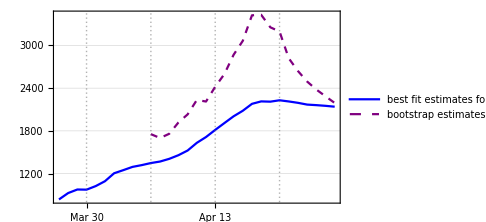

April 26

Croatiadate.txt

Croatiagraf.png

Croatialoggraf.png

Croatiadfgraf.png

Croatiafinalplot.png

country : Czechia

data length : 52

start date : {2020,3,5}

jdp0 : {7216.09,74.357,0.160426}

jp20 : {8085.61,486.719,0.0960938}

backward result : {2216.85,9.55805,0.303903}

forward result : {8085.61,486.719,0.0960938}

last tab: {8085.61,486.719,0.0960938}

backward result : {2216.85,9.55805,0.303903}

forward result : {8085.61,486.719,0.0960938}

past errors : {{85.6312,129.563,123.915,209.616,316.675,409.183,473.321,498.355,558.635,615.584},342.048}

boot tab : {{9746.37,89.0792,0.147415},{8757.52,93.6428,0.147021},{7322.81,77.909,0.158933},{6079.92,47.0909,0.186442},{6848.02,73.7599,0.16362},{7931.86,112.511,0.142321},{8162.42,128.142,0.136611},{8321.56,143.242,0.131976},{8165.76,146.739,0.131839},{7956.08,149.669,0.132238},{7426.67,128.353,0.140741},{7457.47,143.195,0.137005},{7719.14,184.128,0.127089},{7803.91,208.119,0.122653},{7528.09,173.829,0.130412},{7492.7,175.735,0.130394},{7657.59,229.587,0.120863},{7980.6,340.932,0.106464},{8354.69,521.848,0.0914293},{8663.22,700.572,0.0810726},{9307.2,1016.19,0.0671598},{9728.51,1209.91,0.0604686}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

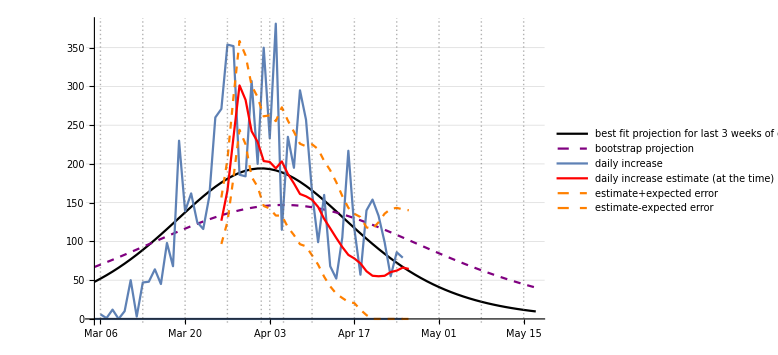

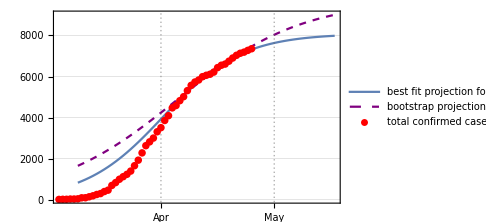

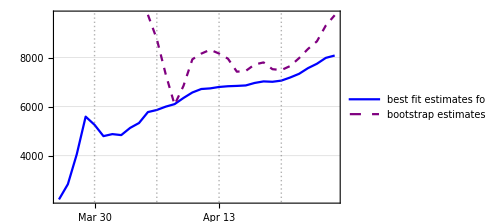

April 26

Czechiadate.txt

Czechiagraf.png

Czechialoggraf.png

Czechiadfgraf.png

Czechiafinalplot.png

country : Sweden

data length : 49

start date : {2020,3,8}

jdp0 : {23138.8,461.923,0.102938}

jp20 : {25714.,622.671,0.0919088}

backward result : {33816.,391.165,0.107741}

forward result : {25714.,622.671,0.0919088}

last tab: {25714.,622.671,0.0919088}

backward result : {33816.,391.165,0.107741}

forward result : {25714.,622.671,0.0919088}

past errors : {{122.541,374.507,579.795,766.213,806.144,1023.59,1402.22,1873.43,2428.38,2803.06},1217.99}

boot tab : {{14328.6,230.525,0.14094},{15189.8,252.891,0.1354},{16812.4,298.978,0.126058},{18482.6,343.08,0.118537},{18921.5,352.548,0.116978},{18681.,340.621,0.118503},{18698.9,343.557,0.118173},{19793.6,391.331,0.112252},{22360.6,500.522,0.101305},{25768.5,630.977,0.0912165},{30601.6,789.143,0.081737},{35234.9,926.372,0.0752642}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49}

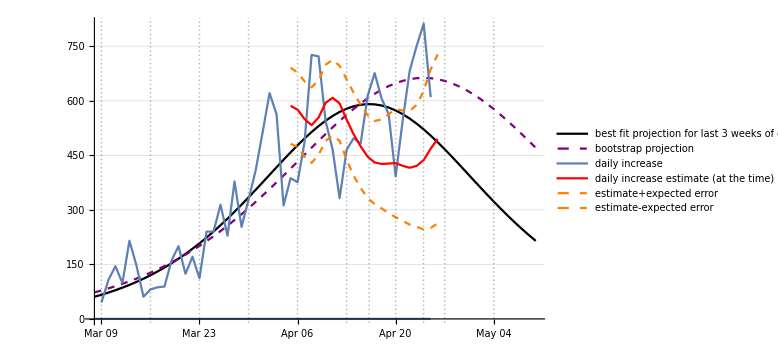

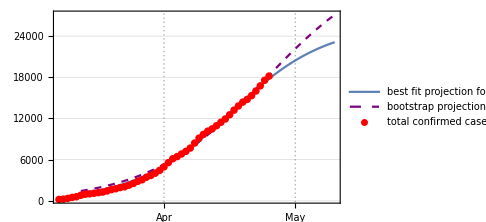

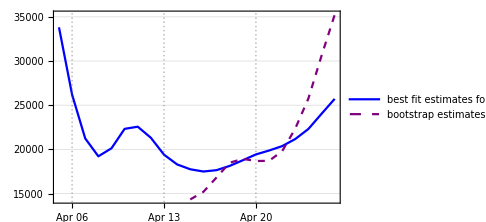

April 26

Swedendate.txt

Swedengraf.png

Swedenloggraf.png

Swedendfgraf.png

Swedenfinalplot.png

country : Greece

data length : 49

start date : {2020,3,8}

jdp0 : {2469.73,97.9217,0.138165}

jp20 : {2546.18,155.115,0.118531}

backward result : {2478.4,89.1455,0.143581}

forward result : {2546.18,155.115,0.118531}

last tab: {2546.18,155.115,0.118531}

backward result : {2478.4,89.1455,0.143581}

forward result : {2546.18,155.115,0.118531}

past errors : {{-15.6396,-21.0574,-29.8293,-47.2259,-52.5005,90.1127,85.3993,130.165,148.233,156.447},44.4104}

boot tab : {{2352.44,85.4084,0.14789},{2343.2,82.2574,0.149785},{2378.88,87.4267,0.14601},{2379.53,86.5441,0.146415},{2374.13,85.708,0.147053},{2332.45,75.2657,0.15395},{2313.2,68.0001,0.158783},{2460.69,105.336,0.135574},{2480.71,114.594,0.131611},{2574.66,155.517,0.116975},{2663.68,207.482,0.103821},{2751.31,268.599,0.0923139}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49}

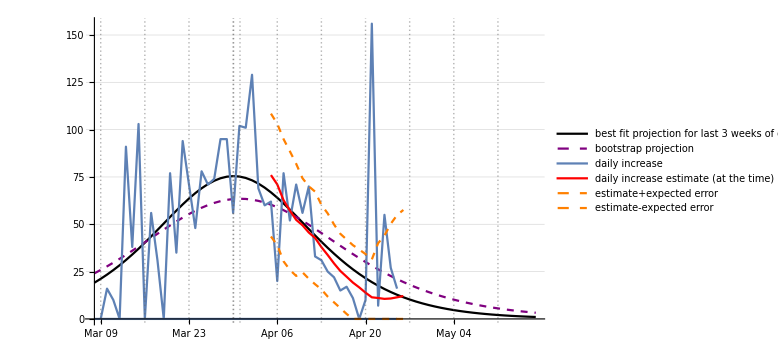

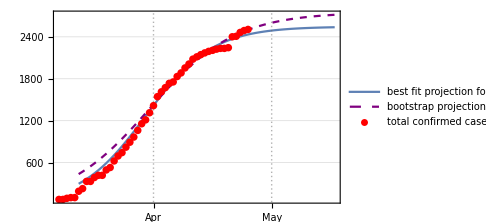

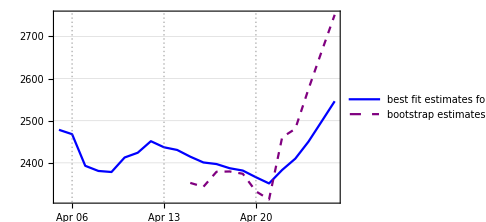

April 26

Greecedate.txt

Greecegraf.png

Greeceloggraf.png

Greecedfgraf.png

Greecefinalplot.png

country : Japan

data length : 37

start date : {2020,3,20}

jdp0 : {17951.8,517.917,0.123382}

jp20 : {16500.2,400.568,0.136712}

backward result : {61680.7,682.989,0.0970644}

forward result : {16500.2,400.568,0.136712}

last tab: {16500.2,400.568,0.136712}

backward result : {61680.7,682.989,0.0970644}

forward result : {16500.2,400.568,0.136712}

past errors : {{-265.822,-642.016,-1573.55,-2221.75,-2885.41,-3123.78,-3809.48,-4604.44},-2390.78}

boot tab : {{13315.9,224.523,0.172372},{12884.9,183.951,0.183025}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37}

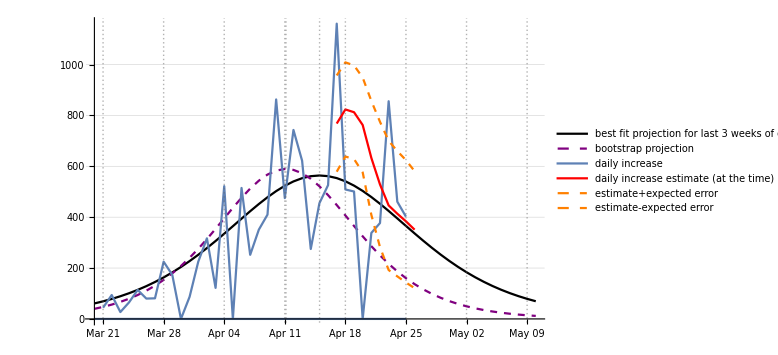

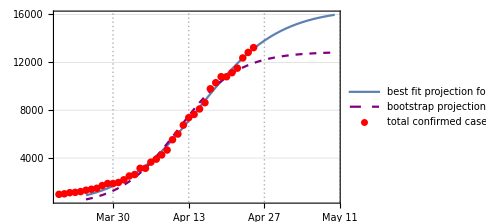

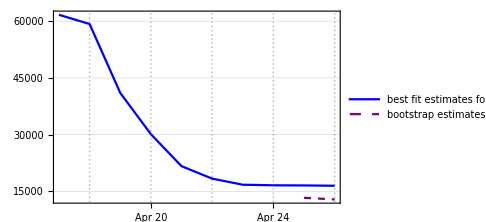

April 26

Japandate.txt

Japangraf.png

Japanloggraf.png

Japandfgraf.png

Japanfinalplot.png

country : Denmark

data length : 39

start date : {2020,3,18}

jdp0 : {9249.18,848.355,0.118097}

jp20 : {9006.69,742.152,0.12699}

backward result : {9622.11,847.804,0.116597}

forward result : {9006.69,742.152,0.12699}

last tab: {9006.69,742.152,0.12699}

backward result : {9622.11,847.804,0.116597}

forward result : {9006.69,742.152,0.12699}

past errors : {{-145.52,-129.885,-126.351,-136.175,-145.752,-94.5793,4.76418,60.6461,100.4,247.345},-36.5107}

boot tab : {{8789.2,690.271,0.132732},{9408.77,861.385,0.115934}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39}

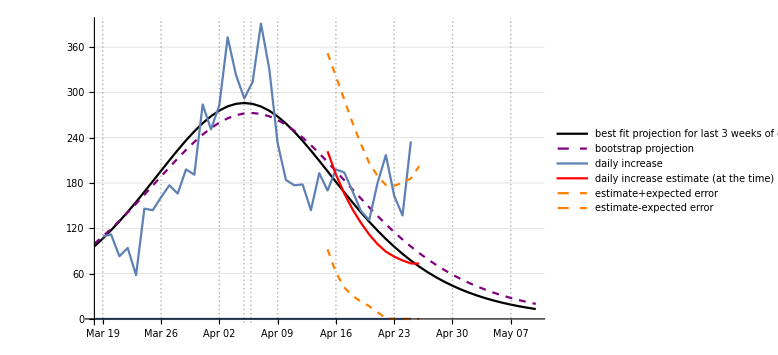

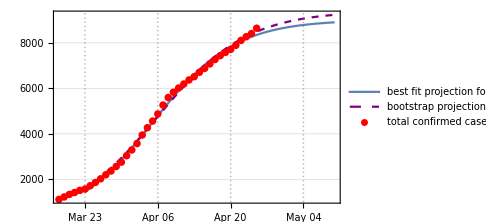

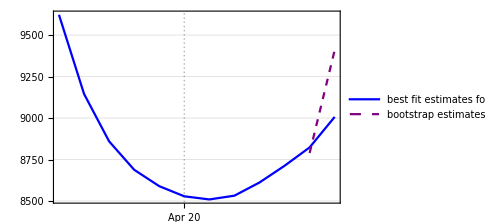

April 26

Denmarkdate.txt

Denmarkgraf.png

Denmarkloggraf.png

Denmarkdfgraf.png

Denmarkfinalplot.png

{29.90911,Null}

```mathematica
countrydateplotlist={};
Timing[
For[cit=1,cit≤Length[countryparameters],cit++,
countrynames=Transpose[countryparameters][[1]];
currentnamme=countrynames[[cit]];
{currentnamme,ctrunc,jdp0,jlag,jprojtime,jbootlag,jplotdrop}=countryparameters[[cit]];
Print["country : ",currentnamme];
countinds=Flatten[Position[countriescsv,currentnamme]];
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}];

truncdatesandata=Select[datesanddata,#[[2]]>ctrunc&];
justdata=Transpose[truncdatesandata][[2]];
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]];
Print["data length : ",Length[justdata]];
Print["start date : ",jstartdate];

{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime];
Print["jdp0 : ",jdp0];
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,jlag,justtime,{1,0}];
Print["jp20 : ",jp20];

(*update jdp0*)
countryparameters[[cit,3]]=jdp0;

{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,jbootabc}=somegraphs[jdp0,jp20,justtime,justdata,jstartdate,jlag,jprojtime,5,jbootlag,wpopulations[[cit]]];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]-1];
Print[jgraf];
Print[jloggraf];
Print[jfinal];

jdatestring=reldatetostring[cpstartdate,timecpert[[-1]]];
Print[jdatestring];

(*new zealand string exception*)
If[currentnamme==="New Zealand",currentnamme="newzealand"];

datefilename=currentnamme<>"date.txt";
Print[datefilename];
Export[datefilename,jdatestring];
graffilename=currentnamme<>"graf.png";
Export[graffilename,jgraf];
Print[graffilename];
loggraffilename=currentnamme<>"loggraf.png";
Export[loggraffilename,jloggraf];
Print[loggraffilename];
dfgraffilename=currentnamme<>"dfgraf.png";
Export[dfgraffilename,jdfpplot];
Print[dfgraffilename];
finalgraffilename=currentnamme<>"finalplot.png";
Export[finalgraffilename,jfinal];
Print[finalgraffilename];

drcases=Transpose[datesanddata][[2]];
drcases=drcases/wpopulations[[cit]];
datesanddata=Transpose[{Transpose[datesanddata][[1]],drcases}];
countrydateplotlist=AppendTo[countrydateplotlist,datesanddata];
]
]
```

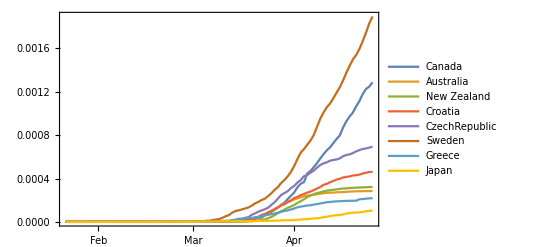

```mathematica
DateListPlot[countrydateplotlist,PlotLegends->wolfcountrynames,PlotRange->All]
```

```mathematica
allcountrynames=Join[fwcountrynames,wolfcountrynames]
%//Length
Length[countrybootabcs]
```

{Slovenia,Italy,Austria,Germany,USA,Canada,Australia,New Zealand,Croatia,CzechRepublic,Singapore,Japan}

12

12

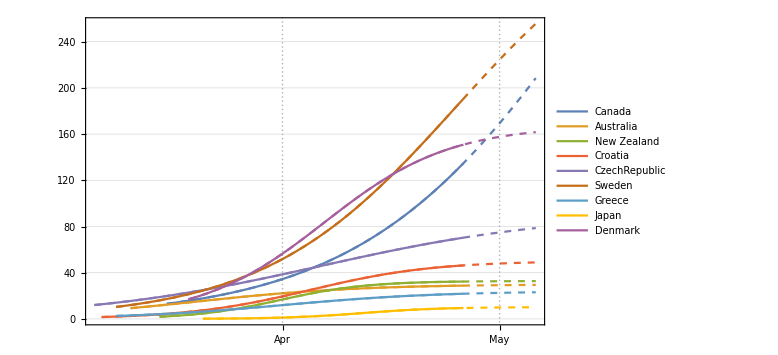

```mathematica
projfwcountryplot=DateListPlot[countrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,countrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->wolfcountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

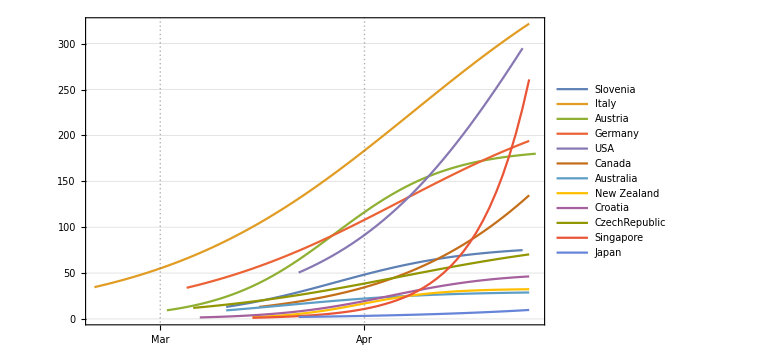

```mathematica
DateListPlot[countrybootabcs,PlotRange->All,PlotLegends->allcountrynames,ImageSize->Large,PlotTheme->"Detailed"]
```

```mathematica
ColorData
```

```mathematica
countinds=Flatten[Position[countriescsv,"Denmark"]]
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}]
```

{94,95,96}

{{{2020,1,22},0},{{2020,1,23},0},{{2020,1,24},0},{{2020,1,25},0},{{2020,1,26},0},{{2020,1,27},0},{{2020,1,28},0},{{2020,1,29},0},{{2020,1,30},0},{{2020,1,31},0},{{2020,2,1},0},{{2020,2,2},0},{{2020,2,3},0},{{2020,2,4},0},{{2020,2,5},0},{{2020,2,6},0},{{2020,2,7},0},{{2020,2,8},0},{{2020,2,9},0},{{2020,2,10},0},{{2020,2,11},0},{{2020,2,12},0},{{2020,2,13},0},{{2020,2,14},0},{{2020,2,15},0},{{2020,2,16},0},{{2020,2,17},0},{{2020,2,18},0},{{2020,2,19},0},{{2020,2,20},0},{{2020,2,21},0},{{2020,2,22},0},{{2020,2,23},0},{{2020,2,24},0},{{2020,2,25},0},{{2020,2,26},0},{{2020,2,27},1},{{2020,2,28},1},{{2020,2,29},3},{{2020,3,1},4},{{2020,3,2},4},{{2020,3,3},6},{{2020,3,4},11},{{2020,3,5},11},{{2020,3,6},24},{{2020,3,7},24},{{2020,3,8},37},{{2020,3,9},92},{{2020,3,10},264},{{2020,3,11},444},{{2020,3,12},617},{{2020,3,13},804},{{2020,3,14},836},{{2020,3,15},875},{{2020,3,16},933},{{2020,3,17},1025},{{2020,3,18},1116},{{2020,3,19},1225},{{2020,3,20},1337},{{2020,3,21},1420},{{2020,3,22},1514},{{2020,3,23},1572},{{2020,3,24},1718},{{2020,3,25},1862},{{2020,3,26},2023},{{2020,3,27},2200},{{2020,3,28},2366},{{2020,3,29},2564},{{2020,3,30},2755},{{2020,3,31},3039},{{2020,4,1},3290},{{2020,4,2},3573},{{2020,4,3},3946},{{2020,4,4},4269},{{2020,4,5},4561},{{2020,4,6},4875},{{2020,4,7},5266},{{2020,4,8},5597},{{2020,4,9},5830},{{2020,4,10},6014},{{2020,4,11},6191},{{2020,4,12},6369},{{2020,4,13},6513},{{2020,4,14},6706},{{2020,4,15},6876},{{2020,4,16},7074},{{2020,4,17},7268},{{2020,4,18},7437},{{2020,4,19},7580},{{2020,4,20},7711},{{2020,4,21},7891},{{2020,4,22},8108},{{2020,4,23},8271},{{2020,4,24},8408},{{2020,4,25},8643}}

```mathematica
truncdatesandata=Select[datesanddata,#[[2]]>1100&]
%//Length
justdata=Transpose[truncdatesandata][[2]]
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]]
```

{{{2020,3,18},1116},{{2020,3,19},1225},{{2020,3,20},1337},{{2020,3,21},1420},{{2020,3,22},1514},{{2020,3,23},1572},{{2020,3,24},1718},{{2020,3,25},1862},{{2020,3,26},2023},{{2020,3,27},2200},{{2020,3,28},2366},{{2020,3,29},2564},{{2020,3,30},2755},{{2020,3,31},3039},{{2020,4,1},3290},{{2020,4,2},3573},{{2020,4,3},3946},{{2020,4,4},4269},{{2020,4,5},4561},{{2020,4,6},4875},{{2020,4,7},5266},{{2020,4,8},5597},{{2020,4,9},5830},{{2020,4,10},6014},{{2020,4,11},6191},{{2020,4,12},6369},{{2020,4,13},6513},{{2020,4,14},6706},{{2020,4,15},6876},{{2020,4,16},7074},{{2020,4,17},7268},{{2020,4,18},7437},{{2020,4,19},7580},{{2020,4,20},7711},{{2020,4,21},7891},{{2020,4,22},8108},{{2020,4,23},8271},{{2020,4,24},8408},{{2020,4,25},8643}}

39

{1116,1225,1337,1420,1514,1572,1718,1862,2023,2200,2366,2564,2755,3039,3290,3573,3946,4269,4561,4875,5266,5597,5830,6014,6191,6369,6513,6706,6876,7074,7268,7437,7580,7711,7891,8108,8271,8408,8643}

{2020,3,18}

```mathematica
jdp0={Max[justdata],700,0.12}
```

{8643,700,0.12}

```mathematica
jdp0={17986.663577976567,576.9474735585374,0.12382285884487645}
```

{17986.7,576.947,0.123823}

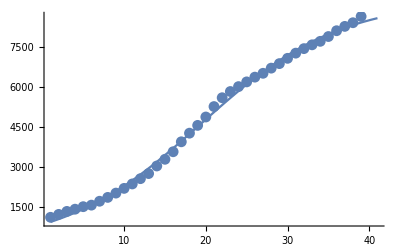

```mathematica
showplots[justdata,jdp0,justtime]
```

```mathematica
{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime]
```

{{9249.18,848.355,0.118097},8,3.86173×10^-7,39}

{9006.69,742.152,0.12699}

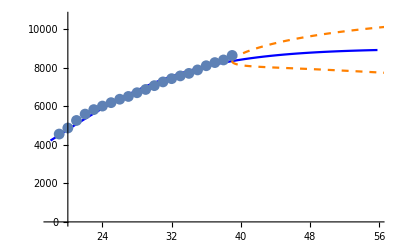
{-Graphics-,73.2651,141.721,235,-20.0208,95.962}

```mathematica
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,28,justtime,{1,0}];
jp20
jpdata20=justdata[[-21;;]];
datastats[jpdata20,jp20,1.8,2,justtime[[-21;;]]]
```

```mathematica
estimates[justdata,jdp0,28,justtime];
```

backward result : {9622.11,847.804,0.116597}

forward result : {9006.69,742.152,0.12699}

```mathematica
?estimates
```

Global`estimates

estimates[tmpdata_,tp0_,lag_,time_]:=Module[{tmp20,tgl,backres,forwp0,forres,abctab,winds},{backres,abctab,winds}=stepGNiteration[tmpdata,tp0,lag,time,{0,-1},{1,Length[time]}];Print[backward result : ,backres];{forres,abctab,winds}=stepGNiteration[tmpdata,backres,lag-1,time,{1,1},{1,lag}];Print[forward result : ,forres];{abctab,winds}]

```mathematica
TableView[Transpose[generatestats[justdata,jdp0,28,justtime,jstartdate]]];
```

{981.19,4.49853,0.341492}

{1452.18,18.7219,0.227054}

{1452.18,18.7219,0.227054}

```mathematica
{"Japan",950,{17986.663577976567,576.9474735585374,0.12382285884487645},21,14,8,0}
```

```mathematica
{name,trunc,cp0,lag,projt,bootl,drop}
```

```mathematica
{"Sweden",200,{23138.83457722449,461.922977379802,0.10293773671900139},28,14,10,0}
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0}
```

```mathematica
{"Denmark",1100,{9249.181828199724,848.3550476707888,0.11809736637519559},28,14,10,0}
```

```mathematica
{"Greece",50,{2469.7252428688025,97.9216579531985,0.1381653045706424},21,14,10,0}
```

{Greece,50,{2469.73,97.9217,0.138165},21,14,10,0}

backward result : {9622.11,847.804,0.116597}

forward result : {9006.69,742.152,0.12699}

last tab: {9006.69,742.152,0.12699}

backward result : {9622.11,847.804,0.116597}

forward result : {9006.69,742.152,0.12699}

past errors : {{-145.52,-129.885,-126.351,-136.175,-145.752,-94.5793,4.76418,60.6461,100.4,247.345},-36.5107}

boot tab : {{8789.2,690.271,0.132732},{9408.77,861.385,0.115934}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39}

April 26

-Graphics-

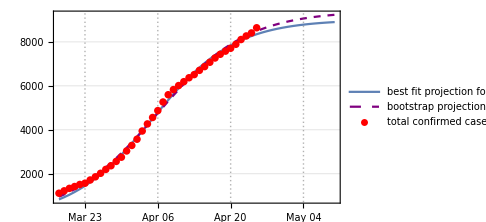

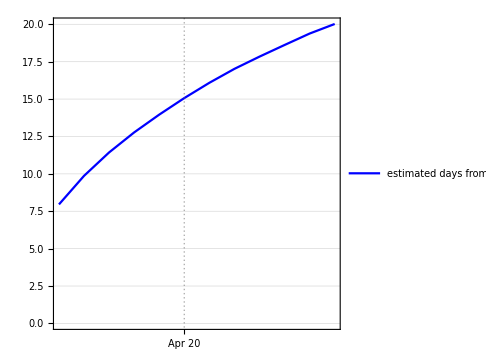

-Graphics-

```mathematica
{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,cboo}=somegraphs[jdp0,jp20,justtime,justdata,jstartdate,28,14,0,10,1000];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]]
jgraf
jloggraf
jdfpplot
jfinal
```